```mathematica
Clear[f,g,h,k,v,ff,gg,hh]
```

```mathematica
f[x_]=FullSimplify[ExpandAll[(8/Pi^2)*Sum[((-1)^(n-1)/(2*n-1)^2)Sin[2*Pi*(2*n-1)*x/(1/2)],{n,1,Infinity}]]]
```

(ⅈ ⅇ^(-4 ⅈ π x) (LerchPhi[-ⅇ^(-8 ⅈ π x),2,1/2]-ⅇ^(8 ⅈ π x) LerchPhi[-ⅇ^(8 ⅈ π x),2,1/2]))/π^2

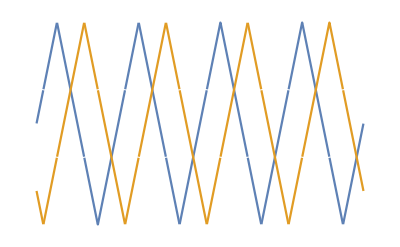

```mathematica
Plot[{f[x],f[x+1/3]},{x,0,2},PlotRange->All,Axes->False]
```

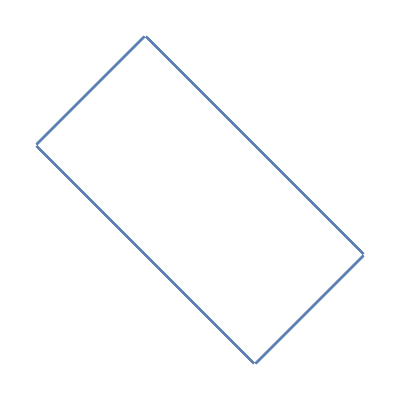

```mathematica
ParametricPlot[{f[x],f[x+1/3]},{x,0,2},PlotRange->All,Axes->False]
```

(ⅈ ⅇ^(-4 ⅈ π Mod[Abs[x],1]) (LerchPhi[-ⅇ^(-8 ⅈ π Mod[Abs[x],1]),2,1/2]-ⅇ^(8 ⅈ π Mod[Abs[x],1]) LerchPhi[-ⅇ^(8 ⅈ π Mod[Abs[x],1]),2,1/2]))/π^2

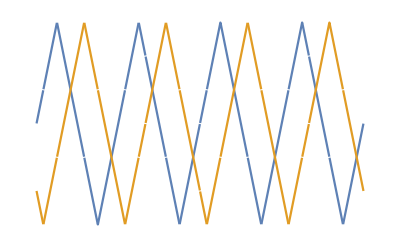

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
Plot[{ff[x],ff[x+1/3]},{x,0,2},PlotRange->All,Axes->False]
```

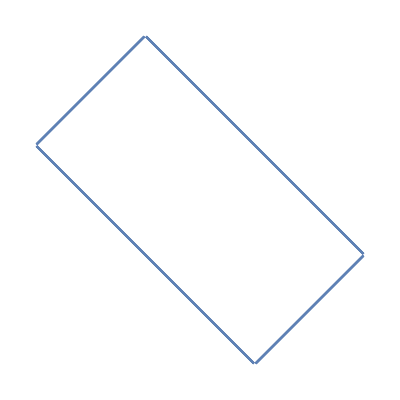

```mathematica
ParametricPlot[{ff[x],ff[x+1/3]},{x,0,2},PlotRange->All,Axes->False]
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
hh[x_]=ParallelSum[ff[2^k*x]/2^(s0*k),{k,0,20}];
kk[x_]=ParallelSum[ff[2^k*(x+1/3)]/2^(s0*k),{k,0,20}];
ll[x_]=ParallelSum[ff[2^k*(x-1/3)]/2^(s0*k),{k,0,20}];
```

```mathematica
aa=Table[Re[hh[t]],{t,0.0001,1,1/2000}];
```

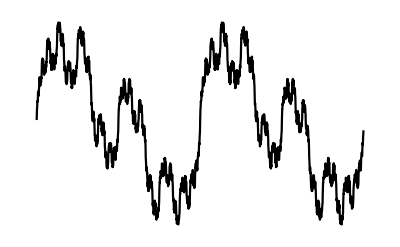

```mathematica
ListLinePlot[aa,PlotStyle->{Black,PointSize[0.0025]},Axes->False]
```

```mathematica
nn=100000.0;
```

```mathematica
bb=ParallelTable[{Re[hh[t]],Re[kk[t]]},{t,0.0001,1,1/nn}];
```

```mathematica
g0=ListPlot[bb,PlotStyle->{PointSize[0.001]},Axes->False,ImageSize->{4000,4000},ColorFunction->Hue,Background->Black];
```

```mathematica
cc=ParallelTable[{Re[hh[t]],Re[kk[t]],Re[ll[t]]},{t,0.0001,1,1/nn}];
```

```mathematica
g1=ListPointPlot3D[cc,PlotStyle->{PointSize[0.001]},Axes->False,ImageSize->{4000,4000},ColorFunction->"Rainbow",ViewPoint->{2,2,2},Background->Black];
```

```mathematica
g2=Show[g1,ViewPoint->Above,ImageSize->2*{2000,2000}];
g3=Show[g1,ViewPoint->{1.3, -2.4, 2.},ImageSize->2*{2000,2000}];

(*g4=Show[g1,ViewPoint->{1.,-2,-2},ImageSize->2*{2000,2000}];*)
Export["Biscuit_zig_zag_100000_4000.jpg",g0];
Export["Biscuit_zig_zag_100000_4000_grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g0}}],"Image",ImageSize->8000]];
(*end*)
```